# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\Spin chain\Unitary operator

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# U(t)

## Choi eigenvalues

```mathematica
tlist=Range[0,5,0.1];
{hx,J}={1,1};
```

```mathematica
L=10;
hz=4.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],VectorFromKetInComputationalBasis[ConstantArray[1,L-1]],RandomChainProductState[L-1]};
styles={Style["Coherent state, h_z = "<>ToString[hz],30,Black],Style["Up state, h_z = "<>ToString[hz],30,Black],Style["Random product state, h_z = "<>ToString[hz],30,Black]};
tf=tlist[[-1]];
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplotsa={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplotsa,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],PlotLabel->styles[[i]],ImageSize->800,AspectRatio->0.5]];
,{i,3}]
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplotsb={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplotsb,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],PlotLabel->styles[[i]],ImageSize->800,AspectRatio->0.5]];
,{i,3}]
```

## Hamiltonian

```mathematica
Clear[U];
U[t_]:=MatrixExp[-I*t*DiagonalMatrix[eigVals]];
```

```mathematica
L=10;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
matrices=ParallelTable[U[t],{t,tlist}];
tracesa=Table[(1/2^L)Abs[Tr[i]],{i,matrices}];
hz=4.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
matrices=ParallelTable[U[t],{t,tlist}];
tracesb=Table[(1/2^L)Abs[Tr[i]],{i,matrices}];
```

```mathematica
plota=ListPlot[{Transpose[{tlist,tracesa}],Transpose[{tlist,tracesb}]},PlotRange->All,Joined->True,PlotMarkers->{Automatic,"OpenMarkers"},PlotStyle->{Directive[Red],Directive[Black]},ImageSize->800,PlotTheme->"Detailed",PlotLegends->{Style["0.5",Red],Style["4.0",Black]},AspectRatio->0.5,PlotLabel->Style["L = "<>ToString[L],30,Black],FrameStyle->Directive[Black,FontSize->20]];
```

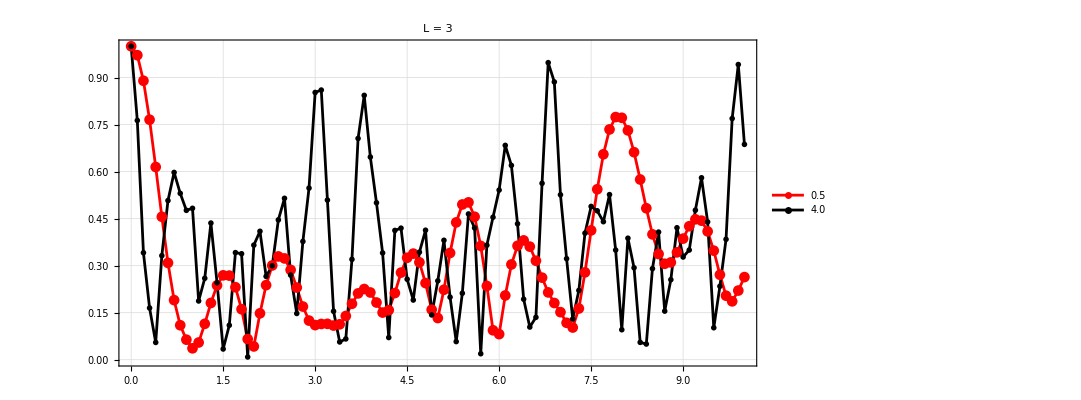
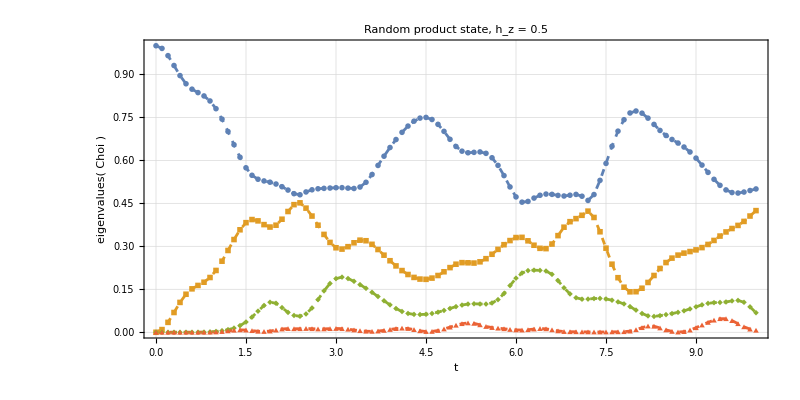
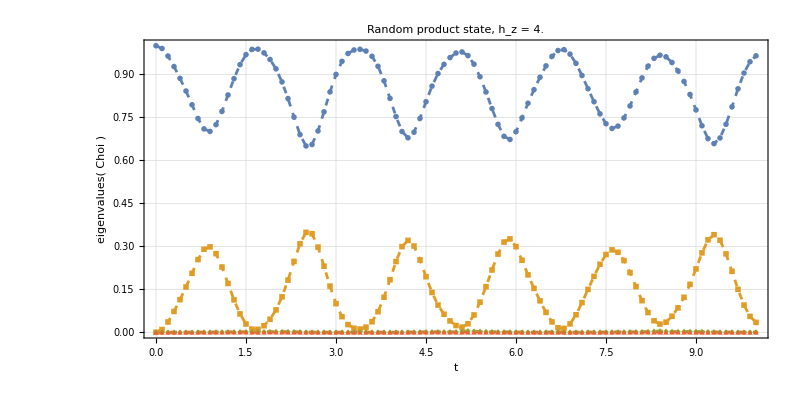

```mathematica
Column[{plota,listplotsa[[3]],listplotsb[[3]]}]
```

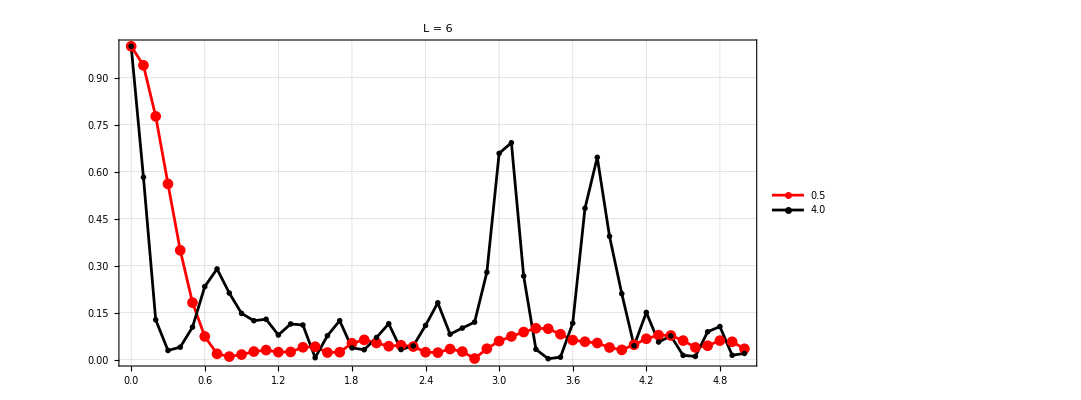
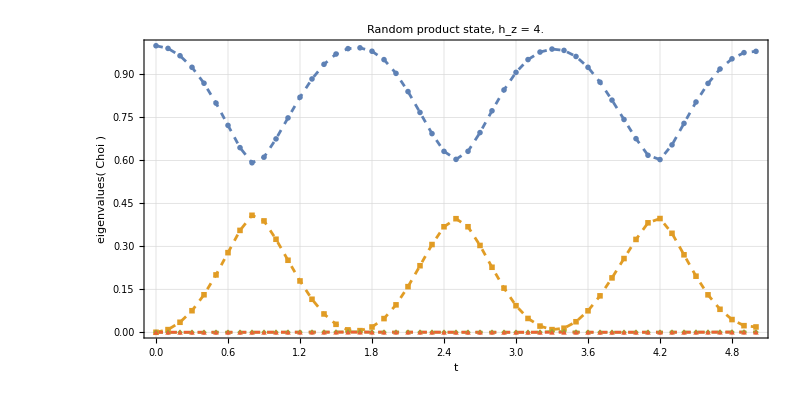
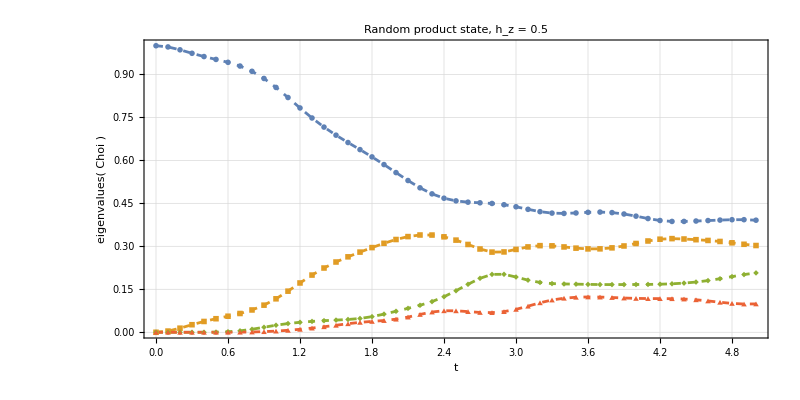

```mathematica
Column[{plota,listplotsa[[3]],listplotsb[[3]]}]
```

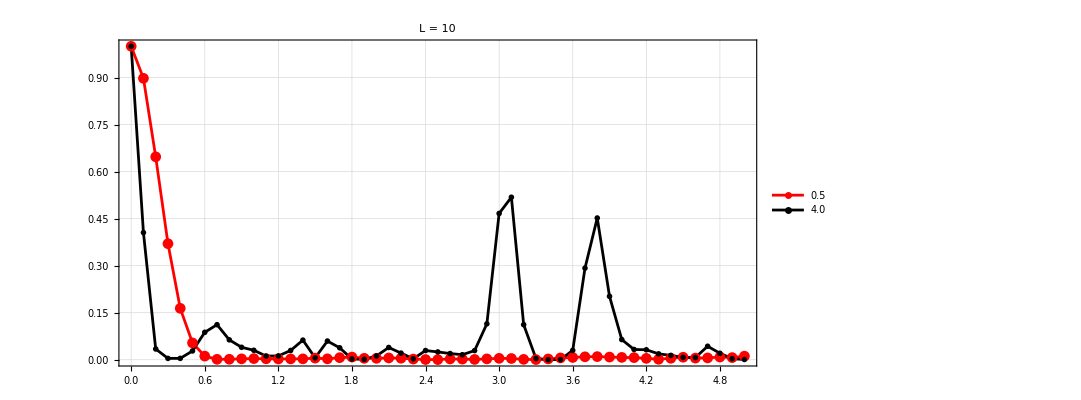
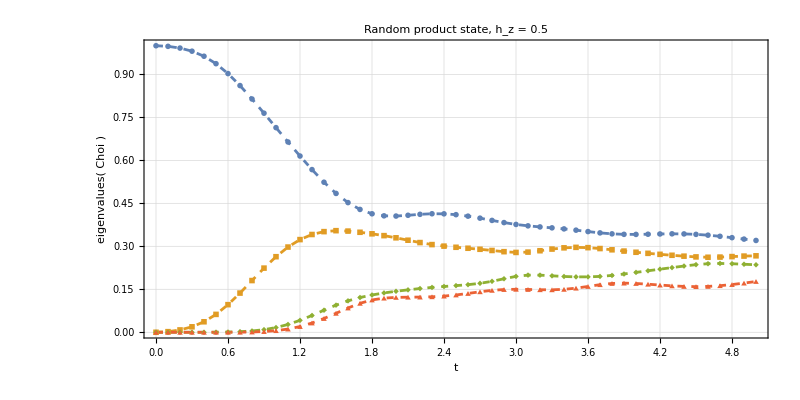
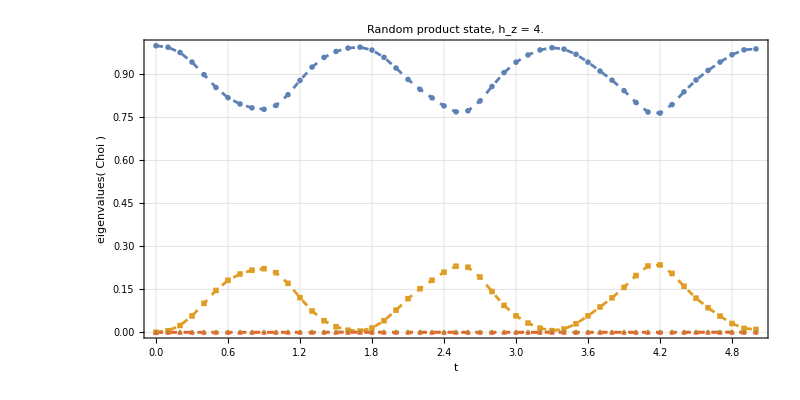

```mathematica
Column[{plota,listplotsa[[3]],listplotsb[[3]]}]
```

```mathematica
mat=(1/2){{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}};
Eigenvalues[mat]//FullSimplify
```

{1,0,0,0}

```mathematica
mat={{Cos[x]^2,0,0,-Sin[x]^2},{0,0,0,0},{0,0,0,0},{-Cos[x]^2,0,0,Sin[x]^2}};
Eigenvalues[mat]//FullSimplify
```

{1,0,0,0}

```mathematica
mat={{a,0,0,b},{0,0,0,0},{0,0,0,0},{c,0,0,d}};
```

```mathematica
Eigenvalues[mat]//FullSimplify
```

{0,0,1/2 (a-√(4 b c+(a-d)^2)+d),1/2 (a+√(4 b c+(a-d)^2)+d)}

```mathematica
mat={{a,0,0,b},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
```

```mathematica
Eigenvalues[mat]//FullSimplify
```

{0,0,0,a}

```mathematica
PermutationMatrix[]
```